```mathematica
ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,gamma1Key],x]//CompleteBaseCoeff
```

{0,0,0,0,0,1586,33088,146892,231967,163709,57997,10874,1080,53,1}

```mathematica
ShowGraph5Least[gamma1Key]
```

-Graphics-296080

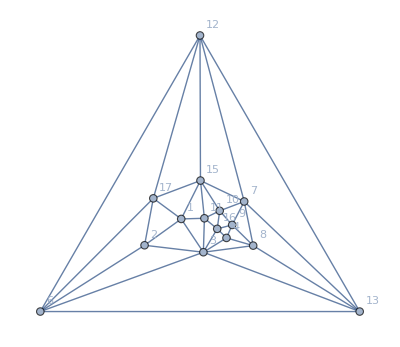
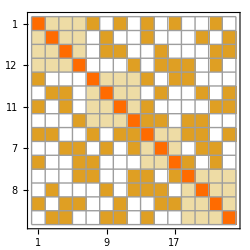
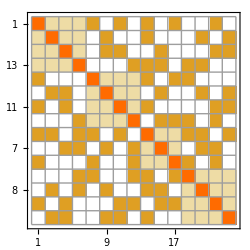
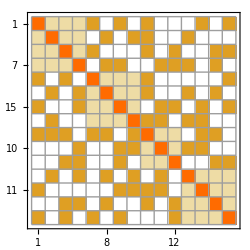
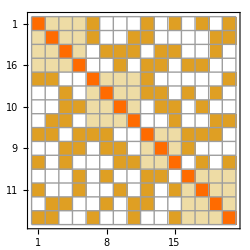
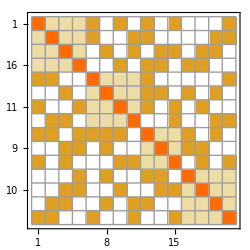
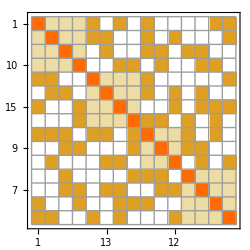
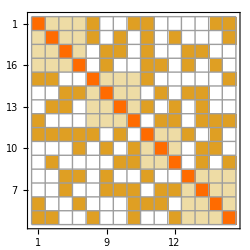
{-Graphics-,{-Graphics-14ac♁29bd♁37h♁68fg,-Graphics-14ad♁29bc♁37h♁68fg,-Graphics-1467♁28fg♁3ac♁9bdh,-Graphics-167g♁28ac♁39f♁4bdh,-Graphics-167g♁28bc♁39f♁4adh,-Graphics-168a♁2dfg♁39c♁47bh,-Graphics-168g♁29df♁3ac♁47bh,-Graphics-18ac♁2dfg♁39h♁467b,-Graphics-18cg♁29df♁3ah♁467b}}

```mathematica
With[
{g=VertexContract[VertexDelete[plantri8,14],{3,5}]},
{Graph[g,VertexLabels->"Name"],
Table[Labeled[DrawSolutionMatrix[g,sol],SymbolToLabel[sol]],{sol,Sort[FindFullFormula4[g],CompareSymbolsNew]}]
}
]
```

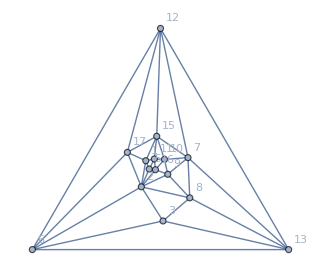
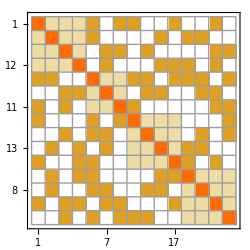
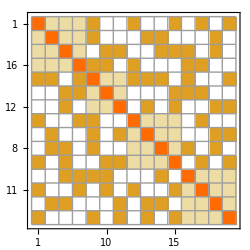
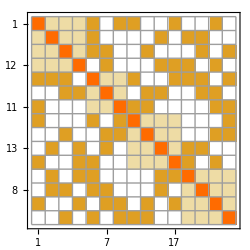
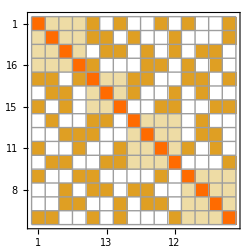
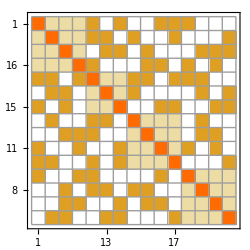
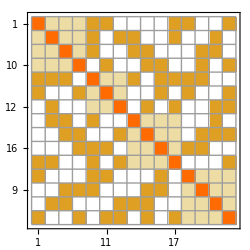
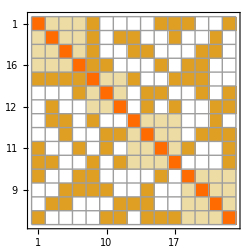
{-Graphics-,{-Graphics-13ac♁27b♁59dh♁68fg,-Graphics-137g♁2ac♁568f♁9bdh,-Graphics-139c♁27b♁5adh♁68fg,-Graphics-167g♁2df♁39bc♁58ah,-Graphics-167g♁2df♁39bh♁58ac,-Graphics-168a♁2bc♁37gh♁59df,-Graphics-168g♁2ac♁37bh♁59df,-Graphics-18ac♁2bd♁37gh♁569f,-Graphics-18cg♁2ad♁37bh♁569f}}

```mathematica
With[
{g=VertexContract[VertexDelete[plantri8,14],{2,4}]},
{Graph[g,VertexLabels->"Name"],
Table[Labeled[DrawSolutionMatrix[g,sol],SymbolToLabel[sol]],{sol,Sort[FindFullFormula4[g],CompareSymbolsNew]}]
}
]
```